### Weierstrass Approx : sin π x

```mathematica
Clear[P];
Module[{n=#},
P[n]=((2n+1)!)/(2^(2n+1)(n!)^2)Integrate[Sin[2u*π]Expand[(1-(u-x)^2)^n],{u,0,1},Assumptions->{x>0,x<1}];
Print["n = ", n,":\t",Collect[P[n],x]];
]&/@{0,1,2,3,4,5,20}
```

n = 0:	0

n = 1:	3/(8 π)-(3 x)/(4 π)

n = 2:	(15 (3+π^2))/(32 π^3)-(45 x)/(16 π^3)-(45 x^2)/(16 π)+(15 x^3)/(8 π)

n = 3:	-(35 (-45-3 π^2-2 π^4))/(128 π^5)-(35 (90-24 π^2) x)/(128 π^5)-(35 (90 π^2+6 π^4) x^2)/(128 π^5)-(35 (-60 π^2+16 π^4) x^3)/(128 π^5)+(525 x^4)/(64 π)-(105 x^5)/(32 π)

n = 4:	(315 (315-15 π^2+2 π^4+π^6))/(512 π^7)+(315 (-630+240 π^2) x)/(512 π^7)+(315 (-630 π^2+30 π^4-4 π^6) x^2)/(512 π^7)+(315 (420 π^2-160 π^4) x^3)/(512 π^7)+(315 (210 π^4-10 π^6) x^4)/(512 π^7)+(315 (-84 π^4+32 π^6) x^5)/(512 π^7)-(2205 x^6)/(128 π)+(315 x^7)/(64 π)

n = 5:	-(693 (-14175+1575 π^2-30 π^4-5 π^6-2 π^8))/(2048 π^9)-(693 (28350-12600 π^2+480 π^4) x)/(2048 π^9)-(693 (28350 π^2-3150 π^4+60 π^6+10 π^8) x^2)/(2048 π^9)-(693 (-18900 π^2+8400 π^4-320 π^6) x^3)/(2048 π^9)-(693 (-9450 π^4+1050 π^6-20 π^8) x^4)/(2048 π^9)-(693 (3780 π^4-1680 π^6+64 π^8) x^5)/(2048 π^9)-(693 (1260 π^6-140 π^8) x^6)/(2048 π^9)-(693 (-360 π^6+160 π^8) x^7)/(2048 π^9)+(31185 x^8)/(1024 π)-(3465 x^9)/(512 π)

$Aborted

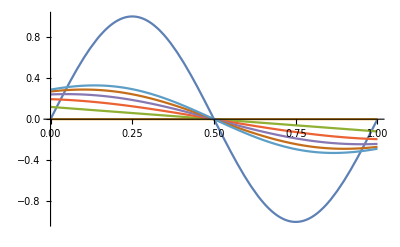

```mathematica
Plot[{Sin[2π*x],P[0],P[1],P[2],P[3],P[4],P[5]},{x,0,1}]
```

```mathematica
Integrate[u*(1-(u-x)^2)^n,{u,0,1/2},Assumptions->{x<1,x>0}]
```

-(4^-n (3-4 (-1+x) x)^(1+n)-4 (1-x^2)^(1+n)+4 (1+n) x ((-1+2 x) Hypergeometric2F1[1/2,-n,3/2,(-1/2+x)^2]-2 x Hypergeometric2F1[1/2,-n,3/2,x^2]))/(8 (1+n))

```mathematica
Integrate[u*(1-(u-x)^2)^n,{u,0,1},Assumptions->{x<1,x>0}]
```

(-(-((-2+x) x))^(1+n)+(1-x^2)^(1+n)+2 (1+n) x (-((-1+x) Hypergeometric2F1[1/2,-n,3/2,(-1+x)^2])+x Hypergeometric2F1[1/2,-n,3/2,x^2]))/(2 (1+n))

```mathematica
Clear[P];
Module[{n=#},
P[n]=((2n+1)!)/(2^(2n+1)(n!)^2)(Integrate[u*(1-(u-x)^2)^n,{u,0,1},Assumptions->{x<1,x>0}]);
Print["n = ", n,":\t",Collect[P[n],x]];
]&/@{0,1,2,3,4,5,20,40}
```

n = 0:	1/4

n = 1:	3/16+x/2-(3 x^2)/8

n = 2:	5/32+x/2+(15 x^2)/32-(5 x^3)/4+(15 x^4)/32

n = 3:	35/256+x/2+(35 x^2)/64-(315 x^4)/128+(35 x^5)/16-(35 x^6)/64

n = 4:	63/512+x/2+(315 x^2)/512-(105 x^4)/256-(63 x^5)/16+(1575 x^6)/256-(105 x^7)/32+(315 x^8)/512

n = 5:	231/2048+x/2+(693 x^2)/1024-(1155 x^4)/2048-(3465 x^6)/512+(231 x^7)/16-(24255 x^8)/2048+(1155 x^9)/256-(693 x^10)/1024

n = 20:	67282234305/1099511627776+x/2+(1412926920405 x^2)/1099511627776-(2354878200675 x^4)/549755813888+(8948537162565 x^6)/549755813888-(57526310330775 x^8)/1099511627776+(152125131763605 x^10)/1099511627776-(41488672299165 x^12)/137438953472+(75226713509475 x^14)/137438953472-(456375395290815 x^16)/549755813888+(581654915566725 x^18)/549755813888-(312256849409505 x^20)/274877906944-(67282234305 x^21)/524288+(335397564665195175 x^22)/274877906944-(5780155583475 x^23)/1048576+(8668850633549030925 x^24)/549755813888-(134228057438475 x^25)/4194304+(26918389940438141145 x^26)/549755813888-(245740597464285 x^27)/4194304+(7714591414157617275 x^28)/137438953472-(2933841826869525 x^29)/67108864+(3840703201635735435 x^30)/137438953472-(1977626712926865 x^31)/134217728+(7055107235800709085 x^32)/1099511627776-(9888133564634325 x^33)/4294967296+(743489210151713025 x^34)/1099511627776-(172578930992325 x^35)/1073741824+(16689021808183725 x^36)/549755813888-(152125131763605 x^37)/34359738368+(261391480274925 x^38)/549755813888-(2354878200675 x^39)/68719476736+(1412926920405 x^40)/1099511627776

n = 40:	53098072606098965203605/1208925819614629174706176+x/2+(2177020976850057573347805 x^2)/1208925819614629174706176-(3628368294750095955579675 x^4)/302231454903657293676544+(28301272699050748453521465 x^6)/302231454903657293676544-(384088700915688729012077025 x^8)/604462909807314587353088+(2210643856381408462536176655 x^10)/604462909807314587353088-(5426125829299820771679706335 x^12)/302231454903657293676544+(22956686200883857110952603725 x^14)/302231454903657293676544-(338228510026355494768035028215 x^16)/1208925819614629174706176+(1094268708908797188955407444225 x^18)/1208925819614629174706176-(195816505804732128549915016335 x^20)/75557863725914323419136+(499289705277000968467099327365 x^22)/75557863725914323419136-(2279366045829787029958496929275 x^24)/151115727451828646838272+(4677960469441439843022515236389 x^26)/151115727451828646838272-(4331444879112444299094921515175 x^28)/75557863725914323419136+(7258904176719475618483213297845 x^30)/75557863725914323419136-(88277641116878784134457142364115 x^32)/604462909807314587353088+(121952178013513471843501399879125 x^34)/604462909807314587353088-(38327827375675662579386154247725 x^36)/151115727451828646838272+(43888906169870424433009749885375 x^38)/151115727451828646838272-(91604024672498783303769067709475 x^40)/302231454903657293676544-(53098072606098965203605 x^41)/549755813888+(569311130903940134248066402189520205 x^42)/302231454903657293676544-(9848428228607403308001975 x^43)/549755813888+(16734706440043426853937297824106636975 x^44)/151115727451828646838272-(2199780741608035447978259325 x^45)/4398046511104+(265850035665853570275587675903245089315 x^46)/151115727451828646838272-(44116762177350716708874134115 x^47)/8796093022208+(7199767550151849472952986386939335674725 x^48)/604462909807314587353088-(1691142550131777473840175141075 x^49)/70368744177664+(25273674172995022303618509215511611981085 x^50)/604462909807314587353088-(2232308166173946265469031186219 x^51)/35184372088832+(6401763083299184136476425567808124638085 x^52)/75557863725914323419136-(28229071798353516294101385047175 x^53)/281474976710656+(7996396746933271018150341196041229646025 x^54)/75557863725914323419136-(56308783428461775888233979697275 x^55)/562949953421312+(12842697800010452884373045141493471569205 x^56)/151115727451828646838272-(1172831517695675274929216319980385 x^57)/18014398509481984+(6811086344964495619130927034871457524725 x^58)/151115727451828646838272-(508834949642590692864264461564625 x^59)/18014398509481984+(1212142484779403494131845406892795844565 x^60)/75557863725914323419136-(1190852320742484182948997880223175 x^61)/144115188075855872+(291704312746515191944653937054133648865 x^62)/75557863725914323419136-(471451798534414559232007958446125 x^63)/288230376151711744+(759137642605499164931951157440451366225 x^64)/1208925819614629174706176-(4024421874445944570835546196011125 x^65)/18446744073709551616+(82775200755887567502132474980876018745 x^66)/1208925819614629174706176-(44653259026486471228851281801895 x^67)/2305843009213693952+(1487116646750599923776343493738996125 x^68)/302231454903657293676544-(20638060894594587542746390748775 x^69)/18446744073709551616+(68466078572305808778279568408200465 x^70)/302231454903657293676544-(1497869115831002905401297982095 x^71)/36893488147419103232+(3863464895262814220678287173760575 x^72)/604462909807314587353088-(2066952005716616912471325172425 x^73)/2361183241434822606848+(62271148813357866568541011832175 x^74)/604462909807314587353088-(24197588157688389927760852575 x^75)/2361183241434822606848+(254664285503624984834270649225 x^76)/302231454903657293676544-(1047147089864877692780294205 x^77)/18889465931478580854784+(838153076087272165738904925 x^78)/302231454903657293676544-(3628368294750095955579675 x^79)/37778931862957161709568+(2177020976850057573347805 x^80)/1208925819614629174706176

{Null,Null,Null,Null,Null,Null,Null,Null}

### Weierstrass Approx : triangle function

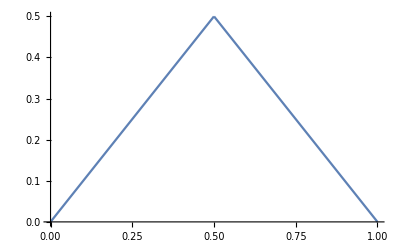

```mathematica
Plot[{If[x<1/2,x,1-x]},{x,0,1}]
```

```mathematica
Clear[P];
Module[{n=#},
P[n]=((2n+1)!)/(2^(2n+1)(n!)^2)(Integrate[u*(1-(u-x)^2)^n,{u,0,1/2},Assumptions->{x<1,x>0}]+Integrate[(1-u)*(1-(u-x)^2)^n,{u,1/2,1},Assumptions->{x<1,x>0}]);
Print["n = ", n,":\t",Collect[P[n],x]];
]&/@{0,1,2,3,4,5,20,40}
```

n = 0:	1/8

n = 1:	17/128+(3 x)/16-(3 x^2)/16

n = 2:	131/1024+(75 x)/256-(15 x^2)/256-(15 x^3)/32+(15 x^4)/64

n = 3:	3957/32768+(735 x)/2048+(175 x^2)/2048-(315 x^3)/512-(385 x^4)/1024+(105 x^5)/128-(35 x^6)/128

n = 4:	29773/262144+(26355 x)/65536+(14805 x^2)/65536-(2835 x^3)/4096-(6195 x^4)/8192+(945 x^5)/2048+(2625 x^6)/2048-(315 x^7)/256+(315 x^8)/1024

n = 5:	448669/4194304+(226149 x)/524288+(186417 x^2)/524288-(93555 x^3)/131072-(303765 x^4)/262144+(6237 x^5)/16384+(20559 x^6)/16384+(3465 x^7)/4096-(45045 x^8)/16384+(3465 x^9)/2048-(693 x^10)/2048

n = 20:	147914493788275539232403/2417851639229258349412352+(301899909003057650501565 x)/604462909807314587353088+(771838217545695046982235 x^2)/604462909807314587353088-(2736984192122845890225 x^3)/37778931862957161709568-(355583477696231606046225 x^4)/75557863725914323419136-(31201619790200443148565 x^5)/18889465931478580854784+(230043153980449976721555 x^6)/18889465931478580854784-(11170950295256948781585 x^7)/2361183241434822606848-(439943370938145250186725 x^8)/9444732965739290427392+(71548295952380074252425 x^9)/2361183241434822606848+(402923569729242969562155 x^10)/2361183241434822606848-(1844748051776825746005 x^11)/36893488147419103232-(33714112444856136300735 x^12)/73786976294838206464-(489449446774534929375 x^13)/18446744073709551616+(16591547079818662958325 x^14)/18446744073709551616+(712495809790936998255 x^15)/2305843009213693952-(25122342370911555054285 x^16)/18446744073709551616-(3794416848419682159675 x^17)/4611686018427387904+(7641125950257444720075 x^18)/4611686018427387904+(418279727625029094825 x^19)/288230376151711744-(981764130771425796795 x^20)/576460752303423488-(285247759249418597775 x^21)/144115188075855872+(1070080768798237418625 x^22)/144115188075855872-(919981521807783209775 x^23)/18014398509481984+(16603931913269641115175 x^24)/72057594037927936-(11565423737298862265835 x^25)/18014398509481984+(22641763689832216458375 x^26)/18014398509481984-(1046314982893625790345 x^27)/562949953421312+(2429336539087298637225 x^28)/1125899906842624-(565935154561304502975 x^29)/281474976710656+(429279018946213441005 x^30)/281474976710656-(33444558093096795645 x^31)/35184372088832+(275705960178482448615 x^32)/562949953421312-(29438494873234021575 x^33)/140737488355328+(10409251626296297775 x^34)/140737488355328-(189181024153786665 x^35)/8796093022208+(89225864047935615 x^36)/17592186044416-(4161069780592725 x^37)/4398046511104+(586364671968075 x^38)/4398046511104-(7064634602025 x^39)/549755813888+(1412926920405 x^40)/2199023255552

n = 40:	128383198953855656028748763203111152838222705415/2923003274661805836407369665432566039311865085952+(365374472478178283485275321239685970203332456109 x)/730750818665451459101842416358141509827966271488+(1315901966885614356869240236601907130234670140035 x^2)/730750818665451459101842416358141509827966271488-(14704162629940177097564383542443975052573225 x^3)/22835963083295358096932575511191922182123945984-(548671118390060274922445714793679236622049652225 x^4)/45671926166590716193865151022383844364247891968-(853821710045192950131905204364580151386085265 x^5)/11417981541647679048466287755595961091061972992+(1063127311665204699719964455622130455873982213455 x^6)/11417981541647679048466287755595961091061972992-(4154618361198345890253305139171786716256528135 x^7)/1427247692705959881058285969449495136382746624-(3697121480858902242312892828511168336561947237275 x^8)/5708990770823839524233143877797980545530986496-(52904588796888451204337364393403984989806507325 x^9)/1427247692705959881058285969449495136382746624+(5120304093377893101381114141864902370904169897025 x^10)/1427247692705959881058285969449495136382746624-(698244493676597656059779384349646090563384375 x^11)/89202980794122492566142873090593446023921664-(3126476726993000135227852701907642275463743837885 x^12)/178405961588244985132285746181186892047843328+(60997540873682985814846301380830207814517569575 x^13)/44601490397061246283071436545296723011960832+(3448333604021093534952476466338710391860517172075 x^14)/44601490397061246283071436545296723011960832-(21254196911955210708076909697675572832063008905 x^15)/5575186299632655785383929568162090376495104-(13158248513348818786998854080031886133819079263965 x^16)/44601490397061246283071436545296723011960832-(151119124022970210507008903674924494654146073015 x^17)/11150372599265311570767859136324180752990208+(10546135304734836845638285647924106330184758734975 x^18)/11150372599265311570767859136324180752990208+(10751226220448362266417603591135114707567601975 x^19)/87112285931760246646623899502532662132736-(445589919189345260301614546592899104745082797565 x^20)/174224571863520493293247799005065324265472-(17280644660278815740613751467112000755476699685 x^21)/43556142965880123323311949751266331066368+(260785427842900659527294323042927136570904880515 x^22)/43556142965880123323311949751266331066368+(3025945429192764948022726116522443470026737625 x^23)/5444517870735015415413993718908291383296-(274574087365189051984729607227803995500230552825 x^24)/21778071482940061661655974875633165533184+(4211951483162618109795818925450245481031021689 x^25)/5444517870735015415413993718908291383296+(135328365500502910381262849284759104999515160939 x^26)/5444517870735015415413993718908291383296-(2324136452838835734297234038209471911264933315 x^27)/340282366920938463463374607431768211456-(32083479946960905829610049986301922684067524725 x^28)/680564733841876926926749214863536422912+(3843952156835372146873438471907165619494942775 x^29)/170141183460469231731687303715884105728+(14694912805337638337267245684002932100007664355 x^30)/170141183460469231731687303715884105728-(1128794275446719821488346900636539633142319805 x^31)/21267647932558653966460912964485513216-(51282226998552216190888743360839768868779526705 x^32)/340282366920938463463374607431768211456+(8562265558385056436605456849848966542112419925 x^33)/85070591730234615865843651857942052864+(20915705414021814118215373288802176890900067275 x^34)/85070591730234615865843651857942052864-(434347432854783341074427761069528560450398535 x^35)/2658455991569831745807614120560689152-(1966872812770561777738064010174787061748276375 x^36)/5316911983139663491615228241121378304+(313967623731176596665961898254851509998490985 x^37)/1329227995784915872903807060280344576+(677148815285775694437744625084463467321114425 x^38)/1329227995784915872903807060280344576-(52224546504798165848593429076411528418220425 x^39)/166153499473114484112975882535043072-(424853730760378799072422809427508085773145105 x^40)/664613997892457936451903530140172288+(65745221125831143997090627374663405206702745 x^41)/166153499473114484112975882535043072+(502922154951524236199130368320554097913897955 x^42)/166153499473114484112975882535043072-(460376772816720881555248593696316650745765425 x^43)/10384593717069655257060992658440192+(8461255310341616684946082264280343055303807725 x^44)/20769187434139310514121985316880384-(12822006773981787836789648166337306901832819975 x^45)/5192296858534827628530496329220096+(56739717750848831704115482397969761836450717285 x^46)/5192296858534827628530496329220096-(24445272743687565822381862610098415253262978575 x^47)/649037107316853453566312041152512+(546611929532993286731689660066507210264026367575 x^48)/5192296858534827628530496329220096-(318326479946600176657808365794647565883906046475 x^49)/1298074214633706907132624082305024+(630288403822968425107171125232170096818031776931 x^50)/1298074214633706907132624082305024-(16821423609958954705178512425329844971720081445 x^51)/20282409603651670423947251286016+(50140744881605042690512455739050504094321231935 x^52)/40564819207303340847894502572032-(16448397282128986936979135733019113631831733625 x^53)/10141204801825835211973625643008+(19139034526773960565230396997835535264653913375 x^54)/10141204801825835211973625643008-(2482721326039281812249978911582717681762081035 x^55)/1267650600228229401496703205376+(9234202713533988250341673960681347466257923415 x^56)/5070602400912917605986812821504-(1930542103880331466622877199693612630543907655 x^57)/1267650600228229401496703205376+(1456227843580191878298555001365472879260512475 x^58)/1267650600228229401496703205376-(62067545266427125642876613271789376945014975 x^59)/79228162514264337593543950336+(76664921105829051907249618495323064709367615 x^60)/158456325028528675187087900672-(10732426733156250878817713449147851941164725 x^61)/39614081257132168796771975168+(5452763914132430093621437320390265761995415 x^62)/39614081257132168796771975168-(314265457845951664423690022243230865599425 x^63)/4951760157141521099596496896+(4206873132377308849829013052431700909102875 x^64)/158456325028528675187087900672-(398879385114078678864118504958916539467095 x^65)/39614081257132168796771975168+(136988893593367923690701591891451980971815 x^66)/39614081257132168796771975168-(1328994222105181406817634089498412283025 x^67)/1237940039285380274899124224+(744173838145197033402193988894700711975 x^68)/2475880078570760549798248448-(46835391821725682361297954359695002825 x^69)/618970019642690137449562112+(10562016495561296751142781564903937975 x^70)/618970019642690137449562112-(265472473671506775778625455679519775 x^71)/77371252455336267181195264+(189281152029937757573646228026585925 x^72)/309485009821345068724781056-(7422358333212679890430652608878525 x^73)/77371252455336267181195264+(1014682841458160074483002000105825 x^74)/77371252455336267181195264-(7457696670199561775735894763615 x^75)/4835703278458516698824704+(1480656551311370707341851498715 x^76)/9671406556917033397649408-(30140855424489047103000360225 x^77)/2417851639229258349412352+(1919406827922800760501648075 x^78)/2417851639229258349412352-(10885104884250287866739025 x^79)/302231454903657293676544+(2177020976850057573347805 x^80)/2417851639229258349412352

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
P[n_]=Integrate[u*(1-(u-x)^2)^n,{u,0,1/2},Assumptions->{x<1,x>0,n∈Integers}]+Integrate[(1-u)*(1-(u-x)^2)^n,{u,1/2,1},Assumptions->{x<1,x>0,n∈Integers}]
```

1/8 ((4^-n (4^(1+n) (-((-2+x) x))^(1+n)-(3-4 (-1+x) x)^(1+n)))/(1+n)+8 (-1+x)^2 Hypergeometric2F1[1/2,-n,3/2,(-1+x)^2]-4 (-1+x) (-1+2 x) Hypergeometric2F1[1/2,-n,3/2,(-1/2+x)^2])+1/8 ((4^-n (-(3-4 (-1+x) x)^(1+n)+(4-4 x^2)^(1+n)))/(1+n)+4 (1-2 x) x Hypergeometric2F1[1/2,-n,3/2,(-1/2+x)^2]+8 x^2 Hypergeometric2F1[1/2,-n,3/2,x^2])

```mathematica
P[n_]:=Integrate[u*(1-(u-x)^2)^n,{u,0,1/2},Assumptions->{x<1,x>0,n∈Integers}]+Integrate[(1-u)*(1-(u-x)^2)^n,{u,1/2,1},Assumptions->{x<1,x>0,n∈Integers}]
```

```mathematica
P[100]
```

$Aborted

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

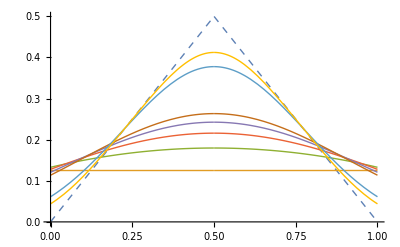

```mathematica
Plot[{If[x<1/2,x,1-x],P[0],P[1],P[2],P[3],P[4],P[20],P[40]},{x,0,1},WorkingPrecision->30,PlotStyle->{{Thick,Dashed},Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick}]
```

```mathematica
Range[0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Clear[P];
Module[{n=#},
P[n]=((2n+1)!)/(2^(2n+1)(n!)^2)(Integrate[u*(1-(u-x)^2)^n,{u,0,1/2},Assumptions->{x<1,x>0}]+Integrate[(1-u)*(1-(u-x)^2)^n,{u,1/2,1},Assumptions->{x<1,x>0}]);
Print["n = ", n,":\t",Collect[P[n],x]];
]&/@{0,1,2,3,4,5,20,40}
```

```mathematica
Integrate[LegendreP[2,x]LegendreP[2,x],{x,-1,1}]
```

2/5

P_2

```mathematica
Function[{nmax},
LegendreExpansionCoefficients[nmax]=((Integrate[LegendreP[#,x]x,{x,-1,1/2}]+Integrate[LegendreP[#,x](1-x),{x,1/2,1}])/Integrate[LegendreP[#,x]LegendreP[#,x],{x,-1,1}])&/@Range[0,nmax];
Print["nmax=",nmax,":\t",LegendreExpansionCoefficients[nmax].(Subscript["P",#]&/@Range[0,nmax])];
LegendreExpansion[nmax,x_]=LegendreExpansionCoefficients[nmax].(LegendreP[#,x]&/@Range[0,nmax]);
]/@{0,1,2,3,4,5,20}
```

nmax=0:	-P_0/8

nmax=1:	-P_0/8+(11 P_1)/16

nmax=2:	-P_0/8+(11 P_1)/16-(45 P_2)/128

nmax=3:	-P_0/8+(11 P_1)/16-(45 P_2)/128-(63 P_3)/256

nmax=4:	-P_0/8+(11 P_1)/16-(45 P_2)/128-(63 P_3)/256-(81 P_4)/1024

nmax=5:	-P_0/8+(11 P_1)/16-(45 P_2)/128-(63 P_3)/256-(81 P_4)/1024+(99 P_5)/2048

nmax=20:	-P_0/8+(11 P_1)/16-(45 P_2)/128-(63 P_3)/256-(81 P_4)/1024+(99 P_5)/2048+(2691 P_6)/32768+(2565 P_7)/65536-(5355 P_8)/262144-(23427 P_9)/524288-(102249 P_10)/4194304+(98325 P_11)/8388608+(977175 P_12)/33554432+(1143315 P_13)/67108864-(16718877 P_14)/2147483648-(89790291 P_15)/4294967296-(219309255 P_16)/17179869184+(193594905 P_17)/34359738368+(4383308637 P_18)/274877906944+(5510700351 P_19)/549755813888-(9486319527 P_20)/2199023255552

{Null,Null,Null,Null,Null,Null,Null}

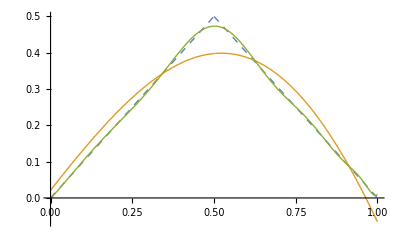

```mathematica
Plot[{If[x<1/2,x,1-x],LegendreExpansion[5,x],LegendreExpansion[20,x]},{x,0,1},WorkingPrecision->30,PlotStyle->{{Thick,Dashed},Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick,Thick}]
```

General::munfl: 0.0000408567^101 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000408567^100 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^102 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

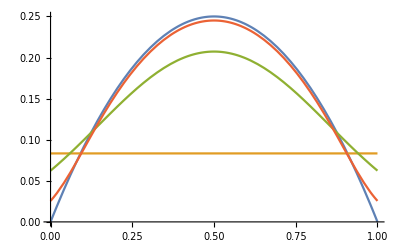

```mathematica
With[{n=300},Plot[{x(1-x),P[0],P[10],P[100]},{x,0,1}]]
```

```mathematica
Integrate[u(1-u)(1-(u-x)^2)^0,{u,0,1},Assumptions->{n∈Integers}]
```

1/6

```mathematica
Integrate[u(1-u)(1-(u-x)^2)^1,{u,0,1},Assumptions->{n∈Integers}]
```

7/60+x/6-x^2/6

```mathematica
Integrate[u(1-u)(1-(u-x)^2)^2,{u,0,1},Assumptions->{n∈Integers}]
```

19/210+x/5-x^2/30-x^3/3+x^4/6

```mathematica
Clear[P];P[n_]:=((2n+1)!)/(2^(2n+1)(n!)^2)*(-((-1+x) Hypergeometric2F1[1/2,-n,3/2,(-1+x)^2])+x Hypergeometric2F1[1/2,-n,3/2,x^2])(*Integrate[(1-(u-x)^2)^n,{u,0,1}]*)
```

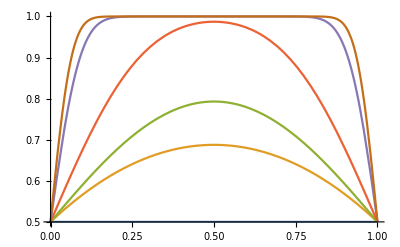

```mathematica
Plot[{P[0],P[1],P[2],P[10],P[100],P[200]},{x,0,1}]
```

```mathematica
P[200]//Expand//N
```

0.5+7.9938 x-532.92 x^3+31815.3 x^5-1.49986×10^6 x^7+5.74531×10^7 x^9-1.84268×10^9 x^11+5.06737×10^10 x^13-1.21713×10^12 x^15+2.59088×10^13 x^17-4.9454×10^14 x^19+8.54613×10^15 x^21-1.34779×10^17 x^23+1.95295×10^18 x^25-2.61506×10^19 x^27+3.25207×10^20 x^29-3.77241×10^21 x^31+4.09749×10^22 x^33-4.1815×10^23 x^35+4.0214×10^24 x^37-3.65454×10^25 x^39+3.14602×10^26 x^41-2.57117×10^27 x^43+1.99902×10^28 x^45-1.48123×10^29 x^47+1.04782×10^30 x^49-7.08738×10^30 x^51+4.59034×10^31 x^53-2.85065×10^32 x^55+1.69949×10^33 x^57-9.73807×10^33 x^59+5.36871×10^34 x^61-2.85067×10^35 x^63+1.45918×10^36 x^65-7.20683×10^36 x^67+3.43722×10^37 x^69-1.5843×10^38 x^71+7.06244×10^38 x^73-3.0469×10^39 x^75+1.27301×10^40 x^77-5.15404×10^40 x^79+2.02328×10^41 x^81-7.70546×10^41 x^83+2.84843×10^42 x^85-1.02257×10^43 x^87+3.56673×10^43 x^89-1.20929×10^44 x^91+3.98715×10^44 x^93-1.27893×10^45 x^95+3.99252×10^45 x^97-1.21348×10^46 x^99+3.59213×10^46 x^101-1.03599×10^47 x^103+2.91198×10^47 x^105-7.97957×10^47 x^107+2.13236×10^48 x^109-5.55845×10^48 x^111+1.41377×10^49 x^113-3.50951×10^49 x^115+8.50485×10^49 x^117-2.01253×10^50 x^119+4.65127×10^50 x^121-1.05015×10^51 x^123+2.31669×10^51 x^125-4.99474×10^51 x^127+1.05261×10^52 x^129-2.16876×10^52 x^131+4.36939×10^52 x^133-8.60932×10^52 x^135+1.6593×10^53 x^137-3.12864×10^53 x^139+5.77197×10^53 x^141-1.04206×10^54 x^143+1.84127×10^54 x^145-3.1846×10^54 x^147+5.39211×10^54 x^149-8.93876×10^54 x^151+1.45097×10^55 x^153-2.30648×10^55 x^155+3.59081×10^55 x^157-5.47555×10^55 x^159+8.17889×10^55 x^161-1.19682×10^56 x^163+1.7158×10^56 x^165-2.41011×10^56 x^167+3.31721×10^56 x^169-4.47407×10^56 x^171+5.9136×10^56 x^173-7.6603×10^56 x^175+9.72538×10^56 x^177-1.21019×10^57 x^179+1.47608×10^57 x^181-1.76477×10^57 x^183+2.06827×10^57 x^185-2.37617×10^57 x^187+2.67617×10^57 x^189-2.95477×10^57 x^191+3.19829×10^57 x^193-3.39392×10^57 x^195+3.53087×10^57 x^197-3.6013×10^57 x^199-6.0307×10^58 x^201+6.35917×10^60 x^202-3.14814×10^62 x^203+1.03378×10^64 x^204-2.53327×10^65 x^205+4.94111×10^66 x^206-7.99051×10^67 x^207+1.10193×10^69 x^208-1.32285×10^70 x^209+1.40432×10^71 x^210-1.33477×10^72 x^211+1.14732×10^73 x^212-8.99269×10^73 x^213+6.47202×10^74 x^214-4.30228×10^75 x^215+2.65507×10^76 x^216-1.52789×10^77 x^217+8.23064×10^77 x^218-4.1648×10^78 x^219+1.98565×10^79 x^220-8.94443×10^79 x^221+3.81606×10^80 x^222-1.54548×10^81 x^223+5.95364×10^81 x^224-2.18565×10^82 x^225+7.65944×10^82 x^226-2.56634×10^83 x^227+8.23305×10^83 x^228-2.53232×10^84 x^229+7.47698×10^84 x^230-2.12171×10^85 x^231+5.79253×10^85 x^232-1.52302×10^86 x^233+3.86022×10^86 x^234-9.43991×10^86 x^235+2.22912×10^87 x^236-5.08685×10^87 x^237+1.12262×10^88 x^238-2.39765×10^88 x^239+4.95898×10^88 x^240-9.93854×10^88 x^241+1.93121×10^89 x^242-3.64047×10^89 x^243+6.66089×10^89 x^244-1.18351×10^90 x^245+2.04308×10^90 x^246-3.42822×10^90 x^247+5.59379×10^90 x^248-8.8793×10^90 x^249+1.37169×10^91 x^250-2.063×10^91 x^251+3.02178×10^91 x^252-4.31217×10^91 x^253+5.99707×10^91 x^254-8.13066×10^91 x^255+1.07495×10^92 x^256-1.38626×10^92 x^257+1.74427×10^92 x^258-2.14196×10^92 x^259+2.5677×10^92 x^260-3.00549×10^92 x^261+3.43576×10^92 x^262-3.83673×10^92 x^263+4.18622×10^92 x^264-4.46366×10^92 x^265+4.65212×10^92 x^266-4.74003×10^92 x^267+4.72234×10^92 x^268-4.601×10^92 x^269+4.38466×10^92 x^270-4.08765×10^92 x^271+3.72846×10^92 x^272-3.32784×10^92 x^273+2.90691×10^92 x^274-2.48537×10^92 x^275+2.08015×10^92 x^276-1.70447×10^92 x^277+1.3675×10^92 x^278-1.07435×10^92 x^279+8.26601×10^91 x^280-6.22893×10^91 x^281+4.59766×10^91 x^282-3.32432×10^91 x^283+2.35475×10^91 x^284-1.63416×10^91 x^285+1.11117×10^91 x^286-7.40348×10^90 x^287+4.83371×10^90 x^288-3.09273×10^90 x^289+1.93927×10^90 x^290-1.19178×10^90 x^291+7.17838×10^89 x^292-4.23789×10^89 x^293+2.45234×10^89 x^294-1.39102×10^89 x^295+7.73419×10^88 x^296-4.2154×10^88 x^297+2.25222×10^88 x^298-1.1796×10^88 x^299+6.05649×10^87 x^300-3.04837×10^87 x^301+1.5041×10^87 x^302-7.2752×10^86 x^303+3.44963×10^86 x^304-1.60345×10^86 x^305+7.3061×10^85 x^306-3.26329×10^85 x^307+1.42876×10^85 x^308-6.13168×10^84 x^309+2.57933×10^84 x^310-1.06348×10^84 x^311+4.29757×10^83 x^312-1.70206×10^83 x^313+6.60639×10^82 x^314-2.51286×10^82 x^315+9.36616×10^81 x^316-3.42074×10^81 x^317+1.2241×10^81 x^318-4.29159×10^80 x^319+1.47399×10^80 x^320-4.95924×10^79 x^321+1.63433×10^79 x^322-5.27508×10^78 x^323+1.66742×10^78 x^324-5.16115×10^77 x^325+1.56418×10^77 x^326-4.64105×10^76 x^327+1.348×10^76 x^328-3.83221×10^75 x^329+1.06621×10^75 x^330-2.90279×10^74 x^331+7.73218×10^73 x^332-2.01484×10^73 x^333+5.1353×10^72 x^334-1.27999×10^72 x^335+3.11956×10^71 x^336-7.43271×10^70 x^337+1.73097×10^70 x^338-3.93947×10^69 x^339+8.76003×10^68 x^340-1.90284×10^68 x^341+4.03676×10^67 x^342-8.36177×10^66 x^343+1.69081×10^66 x^344-3.3367×10^65 x^345+6.42467×10^64 x^346-1.20664×10^64 x^347+2.20991×10^63 x^348-3.94559×10^62 x^349+6.86525×10^61 x^350-1.16377×10^61 x^351+1.92129×10^60 x^352-3.08805×10^59 x^353+4.83031×10^58 x^354-7.35017×10^57 x^355+1.08761×10^57 x^356-1.56427×10^56 x^357+2.18585×10^55 x^358-2.96613×10^54 x^359+3.90664×10^53 x^360-4.99152×10^52 x^361+6.18352×10^51 x^362-7.42262×10^50 x^363+8.62836×10^49 x^364-9.70655×10^48 x^365+1.056×10^48 x^366-1.11022×10^47 x^367+1.1271×10^46 x^368-1.10397×10^45 x^369+1.04235×10^44 x^370-9.47819×10^42 x^371+8.29185×10^41 x^372-6.97149×10^40 x^373+5.62658×10^39 x^374-4.35381×10^38 x^375+3.22566×10^37 x^376-2.28487×10^36 x^377+1.54497×10^35 x^378-9.9552×10^33 x^379+6.10162×10^32 x^380-3.54994×10^31 x^381+1.95616×10^30 x^382-1.0184×10^29 x^383+4.9955×10^27 x^384-2.30171×10^26 x^385+9.92756×10^24 x^386-3.99271×10^23 x^387+1.49074×10^22 x^388-5.14092×10^20 x^389+1.62785×10^19 x^390-4.70015×10^17 x^391+1.22727×10^16 x^392-2.86909×10^14 x^393+5.93121×10^12 x^394-1.06735×10^11 x^395+1.63794×10^9 x^396-2.0839×10^7 x^397+211036. x^398-1598.76 x^399+7.9938 x^400

```mathematica
x
```

1

```mathematica
P[1]
```

2/3+x-x^2

```mathematica
P[2]
```

8/15+x-2 x^3+x^4

```mathematica
P[3]
```

16/35+x-x^3-2 x^4+3 x^5-x^6

```mathematica
Integrate[(1-(u-x)^2)^n,{u,0,1},Assumptions->{x>0,x<1}]
```

-((-1+x) Hypergeometric2F1[1/2,-n,3/2,(-1+x)^2])+x Hypergeometric2F1[1/2,-n,3/2,x^2]

```mathematica
?LegendreP
```

```mathematica
LegendreP[1,x]
```

x

```mathematica
Integrate[LegendreP[1,x]LegendreP[1,x],{x,-1,1}]
```

2/3

```mathematica
Integrate[Sin[x]^2,{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of Sin[x]^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ Sin[x]^2 ⅆx